```mathematica
<<"C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\SpectraFitting.m"
```

Usage Instructions:

1. Get a list of spectra from a directory by using the GetSpecDir[path] function.

2. (Optional) Get an individual spectrum for flatfield correction using the GetSpec[path] function. Divide each spectrum by this flat-field using the SpecDivide[spec,ffspec] function.

3. Initialize a list of guesses using the CoordInit[Spectra,center,d] function, where center is a very preliminary guess for the center point of a generic spectrum and d is the overall spread to zoom in on for further fitting. You should save this guess as a variable.

4. Use the PickGuesses[Spectra,CoordList] command to interactively refine these guesses. CoordList should be the variable you defined in the previous step.

5. Run SingleLorentzianFit[Spectra, Coordlist] to fit each function to a single Lorentzian. Save the output to a variable. More options are coming soon.

6. Use the ShowFits[Spectra, CoordList, Fits, Path] where Fits is the list of fits and Path is the original directory to display all of the fits and important parameters.


If you need additional help, all of the functions have usage instructions that can be queried with two question marks and the name of the function, e.g. ??ShowFits .

## Data input and grooming

Directory where spectra reside. Should be tab separated files, but CSV will probably also work.

```mathematica
DataDir="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS";
```

```mathematica
XPSPath="C:\\Users\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\Example Data\\XPS\\2014-06-17_10048_76_77_79_synchotronsamples.xlsx";
```

```mathematica
XPSSpecs=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
sheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

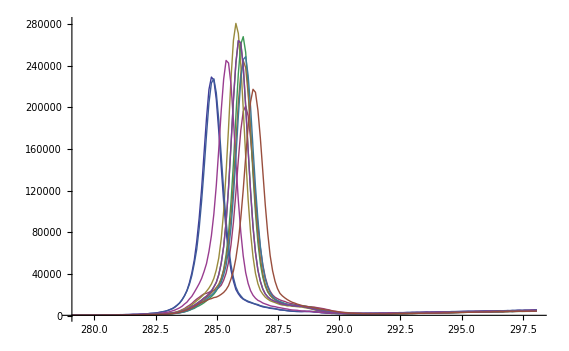

```mathematica
ListLinePlot[XPSSpecs,PlotRange->All]
```

```mathematica
coordlist=CoordInit[XPSSpecs,285,5]
```

{{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}}}

```mathematica
PickGuesses[XPSSpecs,coordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
coordlist
```

{{{285,1000},{280.7,1300.},{290.82,2600.},{290.28,2600.}},{{286.48,4000.},{565/2,1000},{292.01,2600.},{290.84,3000.}},{{285.94,3350.},{565/2,1000},{291.56,2250.},{290.61,2350.}},{{286.48,4100.},{565/2,1000},{291.29,2250.},{290.66,2250.}},{{284.86,3050.},{281.22,1200.},{291.11,2700.},{290.48,2450.}},{{285,1000},{281.49,1500.},{291.15,2250.},{290.43,2450.}},{{285.4,3100.},{565/2,1000},{291.38,2350.},{290.75,2000.}},{{285,1000},{565/2,1000},{291.29,2250.},{290.66,1950.}},{{286.25,6150.},{565/2,1000},{291.29,2300.},{290.43,2550.}},{{285,1000},{565/2,1000},{291.47,2450.},{290.79,2250.}},{{285,1000},{565/2,1000},{291.74,2500.},{290.88,2800.}}}

Pick one spectrum to work with.

```mathematica
data=ChopBoth[XPSSpecs,coordlist][[1]];
```

```mathematica
AllData=ChopBoth[XPSSpecs,coordlist];
```

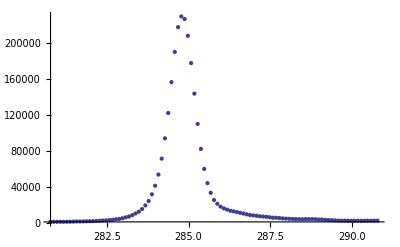

```mathematica
ListPlot[data,PlotRange->All]
```

## Peak fitting XPS data

### Fitting XPS data

#### Simple Fitting

Fit is not very good leaving everything free when the data are far from the origin. Note that the second gaussian is extremely far away from the first, so it has a negligible impact on the fit.

217426. ⅇ^(-2.99934 (-284.808+x)^2)+11142.2 ⅇ^(-5.97738×10^-6 (60.9918+x)^2)

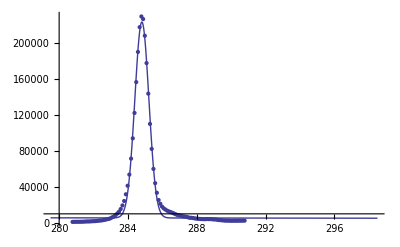

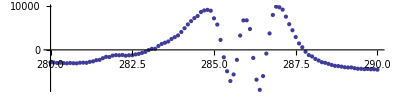

94.5379

```mathematica
nlm=Model[data,2];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"],AspectRatio->0.25,DataRange->{280,290}]
Print[nlm["FitResiduals"]//Total]
```

Centering and normalizing the data does much better. When Mathematica does its optmization routines, it assumes that all parameters are O(1), which means that it has to search a gigantic space. This situation can be somewhat alleviated by picking reasonable guesses (which is performed by Model[] automatically) but it seems that working with the normalized data is the best.

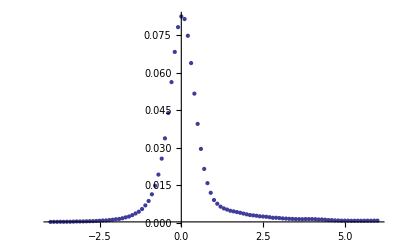

0.000890196 ⅇ^(-0.243997 (-4.93389+x)^2)+0.00479045 ⅇ^(-0.180594 (-0.551007+x)^2)+0.0542504 ⅇ^(-4.93188 (-0.0427552+x)^2)+0.0243921 ⅇ^(-1.6044 (0.0373253+x)^2)

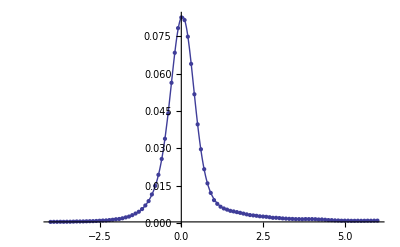

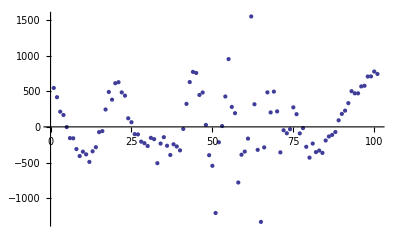

0.00104345

```mathematica
sdata=CenterAndNormalize[data];
ListPlot[sdata,PlotRange->All]
nlm=Model[sdata,4];
nlm[x]
Show[ListPlot[sdata,PlotRange->All],Plot[nlm["Function"][x],{x,-3,3},PlotRange->All]]
ListPlot[nlm["FitResiduals"]*Total[dataᵀ[[2]]]]
Print[(nlm["FitResiduals"]^2//Total)*(60.06/0.1511)]
```

Fit Residuals: 0.00156518

| Weights | Centers
Peak 1
Peak 2
Peak 3
Peak 4 | 0.731514
0.0415963
0.279766
0.0208425 | 0.
0.508252
-0.0800805
4.89113

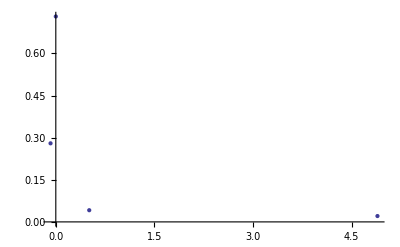

```mathematica
ListPlot[FitSummary[nlm]]
```

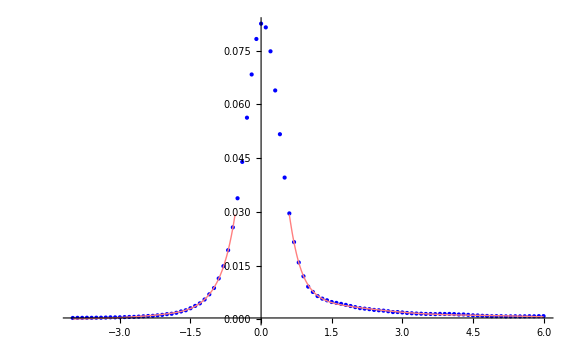
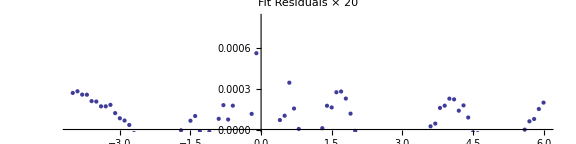

```mathematica
SummaryPlot[sdata,nlm]
```

We can see how the fit improves when adding more gaussians:

```mathematica
Fits=Table[Model[sdata,i],{i,1,6}];
```

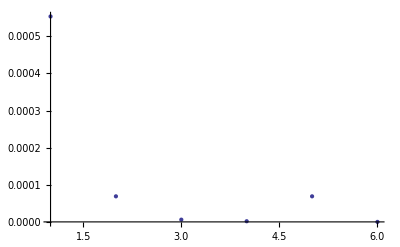

```mathematica
ListPlot[Table[Fits[[i]]["FitResiduals"]^2//Total,{i,1,6}],PlotRange->All]
```

#### Fitting with Voigt profiles

Can also use Voigt profiles. More parameters, trickier to fit. Prone to finding local minima. Not recommended yet.

(221494. 2^(-4.79661 (-284.803+x)^2))/(1-0.48443 (-284.803+x)^2)+(17836. 2^(-0.0489499 (-67.0585+x)^2))/(1-0.0451856 (-67.0585+x)^2)+(948.559 2^(-0.029004 (-20.4369+x)^2))/(1-0.0272774 (-20.4369+x)^2)

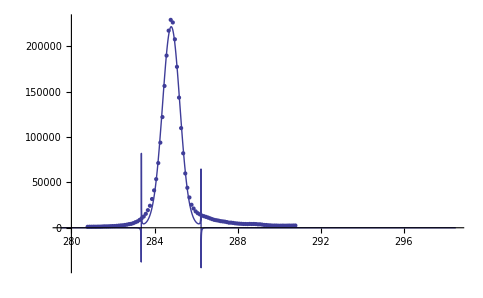

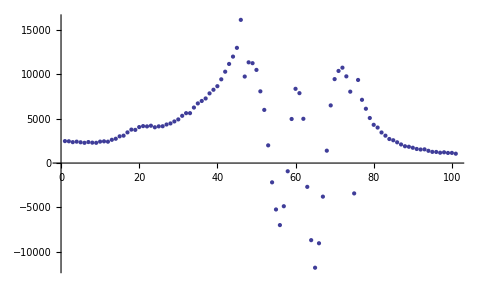

```mathematica
nlm=VoigtModel[data,3];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

#### Fitting by fixing peak positions

Can used knowledge of peak positions with FixedPeaksModel:

279.065 ⅇ^(-0.0000577052 (-288.102+x)^2)+444.521 ⅇ^(-0.0000112515 (-287.002+x)^2)+12323. ⅇ^(-0.128642 (-285.802+x)^2)+213264. ⅇ^(-3.24599 (-284.802+x)^2)

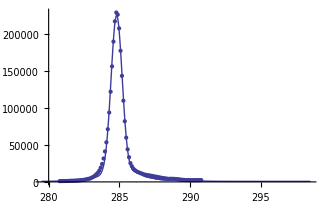

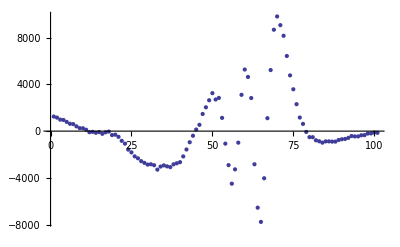

```mathematica
nlm=FixedPeaksModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

#### Fitting with fixed peaks voigt profile

Can used knowledge of peak positions with FixedPeaksModel:

(0.0248885 2^(0.0000582317 (-938.197+x)^2))/(1+0.0000593864 (-938.197+x)^2)

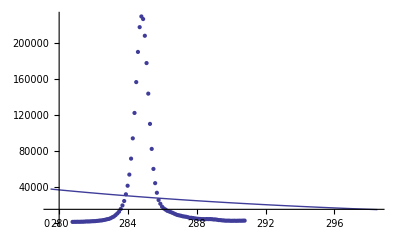

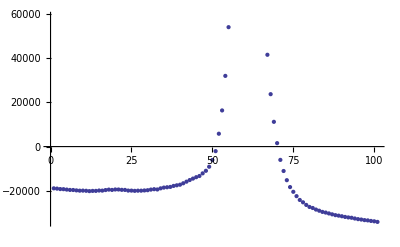

```mathematica
nlm=FixedPeaksVoigtModel[data,{0}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

(1066.75 2^(-60.6086 (-319.713+x)^2))/(1-60.5002 (-319.713+x)^2)+(1.07972×10^6 2^(-0.00330268 (-318.613+x)^2))/(1-0.0000242776 (-318.613+x)^2)+(4.24744×10^6 2^(-0.00451086 (-317.413+x)^2))/(1-0.0044639 (-317.413+x)^2)+(531686. 2^(-0.125433 (-316.413+x)^2))/(1-0.125212 (-316.413+x)^2)

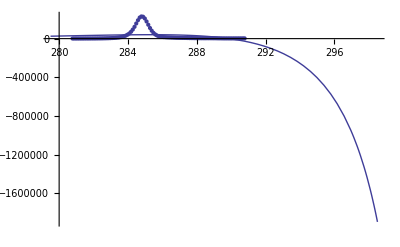

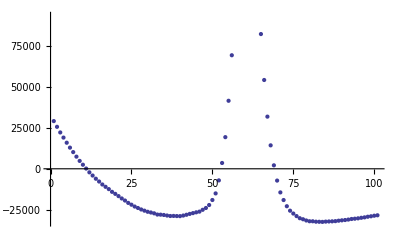

```mathematica
nlm=FixedPeaksVoigtModel[data,{-1,0,1.2,2.3}];
nlm[x]
Show[Plot[nlm["Function"][x],{x,-9.5+289,9.5+289},PlotRange->All],ListPlot[data,PlotRange->All]]
ListPlot[nlm["FitResiduals"]]
```

### Fitting example data

Example peak positions for a carbon 1s edge:

0.0036 ⅇ^(-5.55556 (-2.3+x)^2)+0.0036 ⅇ^(-5.55556 (-1.2+x)^2)+0.3249 ⅇ^(-5.55556 x^2)+0.0441 ⅇ^(-5.55556 (0.9+x)^2)+0.01 ⅇ^(-5.55556 (1.8+x)^2)

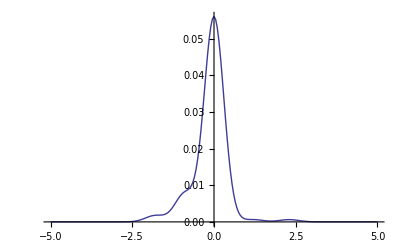

```mathematica
exweights={.10,.21,.57,.06,.06};
expositions={-1.8,-0.9,0,1.2,2.3};
ExampleCFn[x_]:=Table[gfn[exweights[[i]],expositions[[i]],0.3,x],{i,1,Length[exweights]}]//Total
Print[ExampleCFn[x]]
ExampleCData=CenterAndNormalize@Table[{x,ExampleCFn[x]+0*RandomReal[]},{x,-5,5,0.05}];
ListLinePlot[ExampleCData,PlotRange->{{-5,5},All}]
```

0.000495078 ⅇ^(-0.577205 (-1.57938+x)^2)+0.0558349 ⅇ^(-5.59817 (0.000301553+x)^2)+0.00759303 ⅇ^(-5.41049 (0.897706+x)^2)+0.00171306 ⅇ^(-5.726 (1.80639+x)^2)+0.2361 ⅇ^(-7.23886 (6.49486+x)^2)

Sum of Squares of Residuals: 1.172628663250082e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3
Peak 4
Peak 5 | 0.790662
0.0239065
1.84883
0.286643
0.140064 | 6.49456
8.07424
0.
5.59715
4.68847

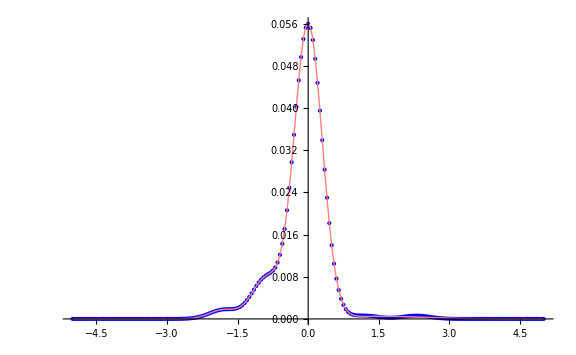
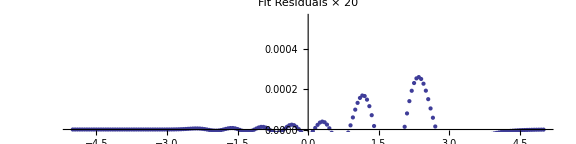

```mathematica
ExCModel=Model[ExampleCData,5]; ExCModel[x]
FitSummary[ExCModel];
SummaryPlot[ExampleCData,ExCModel]
```

```mathematica
FitSummary[data,nlm]
```

Weights | Positions | σs
0.78309 | 0.0427552 | -0.318404
0.0132321 | 0.551007 | -1.66392
0.20082 | -0.0373253 | -0.55825
0.00285812 | 4.93389 | -1.43151

{{0.78309,0.0427552,-0.318404},{0.0132321,0.551007,-1.66392},{0.20082,-0.0373253,-0.55825},{0.00285812,4.93389,-1.43151}}

## Fit all data quickly

### Carbon Peak

```mathematica
RawCData=GetSpec[XPSPath,"Excel XPS","C1s"];
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

11 spectra in all.

Importing Sheet C1s Scan J

Importing Sheet C1s Scan I

Importing Sheet C1s Scan H

Importing Sheet C1s Scan G

Importing Sheet C1s Scan F

Importing Sheet C1s Scan E

Importing Sheet C1s Scan D

Importing Sheet C1s Scan C

Importing Sheet C1s Scan B

Importing Sheet C1s Scan A

Importing Sheet C1s Scan

Formatting XPS Spectra

```mathematica
CSheets=GetSheets[XPSPath,"C1s"]
```

Removing sheets that do not contain the string "C1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{C1s Scan J,C1s Scan I,C1s Scan H,C1s Scan G,C1s Scan F,C1s Scan E,C1s Scan D,C1s Scan C,C1s Scan B,C1s Scan A,C1s Scan}

```mathematica
Ccoordlist=CoordInit[RawCData,285,5]
```

{{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}},{{285,1000},{565/2,1000},{575/2,1000},{1135/4,1000}}}

```mathematica
PickGuesses[RawCData,Ccoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
CData=UserRemoveAve[RawCData,Ccoordlist];
```

```mathematica
CenteredCData=CenterAndNormalize/@CData;
```

```mathematica
AllCModels=FixedPeaksModel[#,{-1.8,-0.9,0,1.2,2.3}]&/@CenteredCData;
```

```mathematica
AllCModels=Model[#,5]&/@CenteredCData;
```

Weights | Means | σs
0.790566 | -31.685 | 2.43767
0.000776804 | 1.05857 | 1.35391
0.135597 | -29.5155 | 0.60045
0.0619759 | 0.0407194 | 0.327729
0.011085 | -0.0689719 | 0.626725

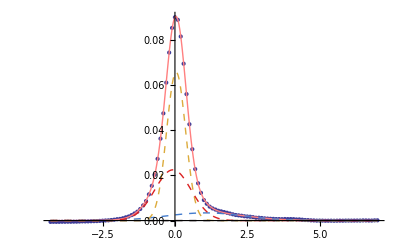

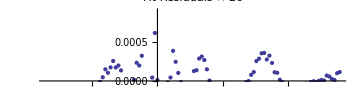

Weights | Means | σs
0.00406904 | -1.47382 | 0.609678
0.00103844 | 1.3498 | 1.30515
0.0162015 | 0.0165098 | 0.524999
0.925536 | -0.674264 | 0.00245871
0.0531546 | -0.0165545 | 0.316264

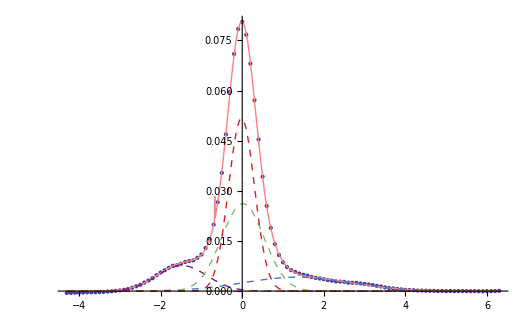

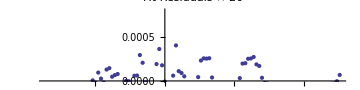

Weights | Means | σs
0.429926 | 0.0236581 | 0.313275
0.0284597 | -0.116533 | 0.912791
0.536341 | 14.3419 | -1.25486
0.00527367 | 2.51741 | -0.699911
3.06338×10^-17 | -4.97259 | -3.10231

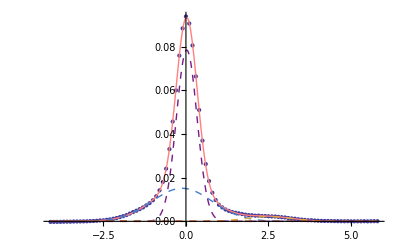

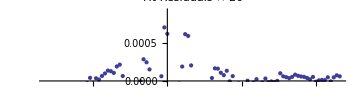

Weights | Means | σs
0.0498714 | -0.143175 | 0.932902
1.40391×10^-13 | 1.3676 | -2.47695
0.0113678 | 2.35079 | -0.743157
0.196211 | -0.0419749 | -0.21839
0.74255 | -0.00532123 | -0.342667

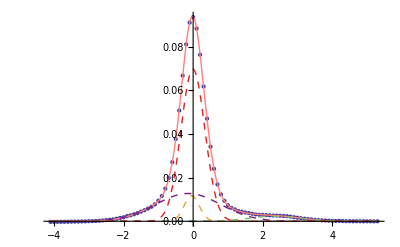

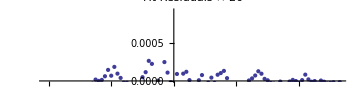

Weights | Means | σs
0.330116 | -0.034547 | -0.350301
1.1809×10^-16 | -3.92099 | -0.827215
0.647824 | -5.35754 | -0.0584714
1.87132×10^-16 | 0.756264 | -0.426442
0.0220605 | -0.0134698 | 0.966716

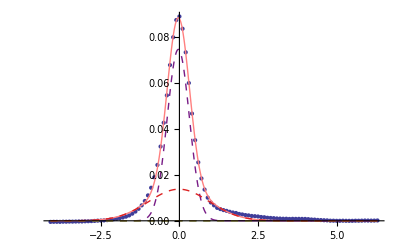

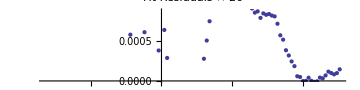

Weights | Means | σs
0.00494253 | -1.78284 | -0.39358
0.00842797 | 1.18918 | 1.27369
0.64878 | 0.0588334 | 0.340099
0.106077 | -0.257738 | -0.717105
0.231773 | 0.0439478 | 0.238272

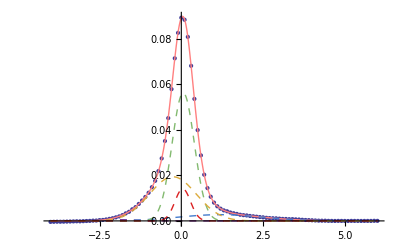

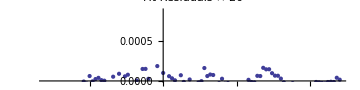

Weights | Means | σs
0.00180597 | 0.018935 | -0.334209
2.17406×10^-18 | -1.59715 | -0.195264
0.998106 | 0.871867 | -0.000292743
0.000087644 | -0.0956447 | -1.13583
5.37651×10^-19 | -2.46488 | -3.19873

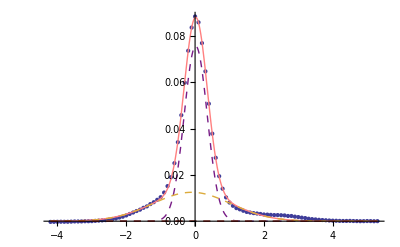

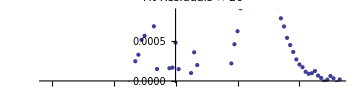

Weights | Means | σs
0.00311711 | -0.0790375 | -0.947267
0.00070246 | 2.52753 | -0.671144
0.945398 | 23.6746 | 0.880313
4.81036×10^-19 | -6.03014 | -19.7966
0.0507827 | 0.0489477 | 0.321718

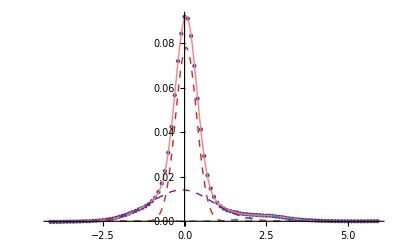

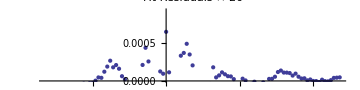

Weights | Means | σs
0.00127197 | -0.1708 | -0.98278
4.78021×10^-19 | -10.6696 | 11.0521
0.978466 | -14.8753 | -0.652697
0.000314469 | 2.51131 | 0.606252
0.0199472 | -0.0320092 | -0.331159

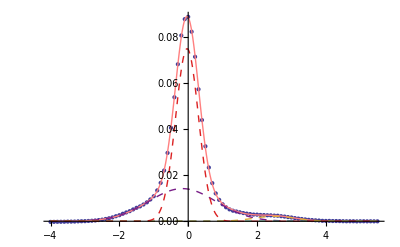

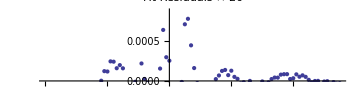

Weights | Means | σs
0.00941089 | -1.72789 | -0.440759
0.0110882 | 2.23567 | 0.858151
0.0656136 | -0.103496 | 0.831901
0.73361 | 0.0587285 | 0.33614
0.180278 | 0.0109658 | 0.229049

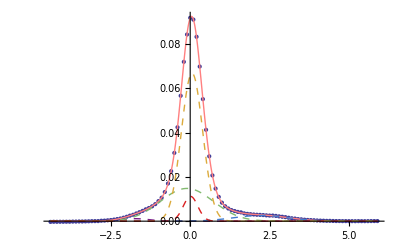

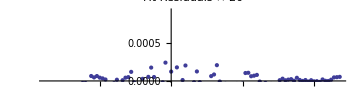

Weights | Means | σs
0.821016 | 0.0407798 | -0.339003
3.31104×10^-14 | 4.88999 | -1.15702
0.130265 | -0.116853 | 0.65441
0.0138904 | 1.16956 | 1.24588
0.0348289 | -1.82018 | 0.564375

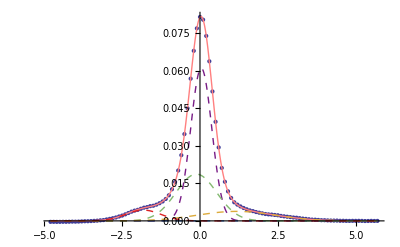

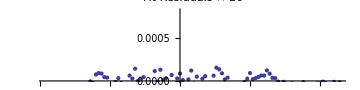

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[FitSummary[CenteredCData[[x]],AllCModels[[x]]],{x,1,Length[CenteredCData],1}]
```

```mathematica
CSummaries=FitSummary/@AllCModels
```

Sum of Squares of Residuals: 9.337931381746313e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.744997
0.219022
0.0230379 | 0.
-0.0640509
1.19796

Sum of Squares of Residuals: 0.000015789585047125255

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0795468
0.023437
0.721449 | -0.44238
1.87065
0.

Sum of Squares of Residuals: 0.000010970222737805098

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0223058
0.135311
0.861331 | 0.971339
-0.187734
0.

Sum of Squares of Residuals: 0.00005383384241342219

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 2.58181×10^-9
0.0635709
0.828646 | -1.58636
0.0750563
0.

Sum of Squares of Residuals: 0.0000920144126208608

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0382415
0.062949
0.724613 | -4.19605
0.175594
0.

Sum of Squares of Residuals: 0.00009023546909026901

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.135727
2.00144×10^-8
0.795269 | -0.18473
1.01665
0.

Sum of Squares of Residuals: 0.00006019181283445589

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.791119
0.0747629
0.0761596 | 0.
129.111
-0.0820984

Sum of Squares of Residuals: 6.510892821174428e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.837577
0.128519
0.0276942 | 0.
-0.19911
0.744366

Sum of Squares of Residuals: 0.000058275679475750086

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 4.95669×10^-9
0.0710014
0.784082 | -3.8044
-0.0425006
0.

Sum of Squares of Residuals: 7.977349352352567e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.836407
0.127068
0.0261622 | 0.
-0.195457
0.811453

Sum of Squares of Residuals: 0.000029385877439711428

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0630375
0.7012
0.0419677 | -0.163819
0.
-4.90177

{{{1.19796,0.0230379},{-0.0640509,0.219022},{0.,0.744997}},{{1.87065,0.023437},{-0.44238,0.0795468},{0.,0.721449}},{{0.971339,0.0223058},{-0.187734,0.135311},{0.,0.861331}},{{-1.58636,2.58181×10^-9},{0.0750563,0.0635709},{0.,0.828646}},{{-4.19605,0.0382415},{0.175594,0.062949},{0.,0.724613}},{{1.01665,2.00144×10^-8},{-0.18473,0.135727},{0.,0.795269}},{{129.111,0.0747629},{-0.0820984,0.0761596},{0.,0.791119}},{{0.744366,0.0276942},{-0.19911,0.128519},{0.,0.837577}},{{-3.8044,4.95669×10^-9},{-0.0425006,0.0710014},{0.,0.784082}},{{0.811453,0.0261622},{-0.195457,0.127068},{0.,0.836407}},{{-4.90177,0.0419677},{-0.163819,0.0630375},{0.,0.7012}}}

Visualize location of peaks and weights:

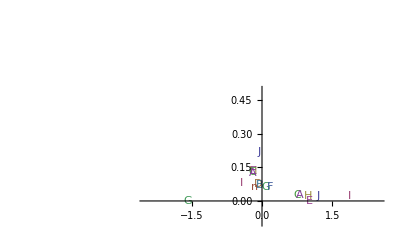

```mathematica
ListPlot[CSummaries,PlotRange->{{-2.5,2.5},{-0.1,0.5}},PlotMarkers->(StringTake[#,-1]&/@CSheets)]
```

#### Oxygen Edge

### Oxygen Peak

```mathematica
RawOData=GetSpec[XPSPath,"Excel XPS","O1s"];
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

11 spectra in all.

Importing Sheet O1s Scan J

Importing Sheet O1s Scan I

Importing Sheet O1s Scan H

Importing Sheet O1s Scan G

Importing Sheet O1s Scan F

Importing Sheet O1s Scan E

Importing Sheet O1s Scan D

Importing Sheet O1s Scan C

Importing Sheet O1s Scan B

Importing Sheet O1s Scan A

Importing Sheet O1s Scan

Formatting XPS Spectra

```mathematica
OSheets=GetSheets[XPSPath,"O1s"]
```

Removing sheets that do not contain the string "O1s"

Here is a list of sheets that are being kept. The order of the original Excel file is being preserved.

11 spectra in all.

{O1s Scan J,O1s Scan I,O1s Scan H,O1s Scan G,O1s Scan F,O1s Scan E,O1s Scan D,O1s Scan C,O1s Scan B,O1s Scan A,O1s Scan}

```mathematica
Ocoordlist=CoordInit[RawOData,532.5,7,12000]
```

{{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}},{{532.5,12000},{529.,12000},{536.,12000},{530.75,12000}}}

```mathematica
PickGuesses[RawOData,Ocoordlist]
```

Part::partw: Part 2 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 3 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

Part::partw: Part 4 of {"2014-06-17_10048_76_77_79_synchotronsamples.xlsx"} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{,,,,,,,,,,}

```mathematica
OData=UserRemoveAve[RawOData,Ocoordlist];
```

```mathematica
CenteredOData=CenterAndNormalize/@OData;
```

```mathematica
AllOModels=FixedPeaksModel[#,{-1.8,-0.9,0,1.2,2.3}]&/@CenteredOData;
```

```mathematica
AllOModels=Model[#,4]&/@CenteredOData;
```

Weights | Means | σs
0.894722 | -7.33885 | -0.293727
0.0583966 | -0.146371 | 0.575256
8.74378×10^-16 | -11.7799 | -6.05926
0.0468818 | 0.275151 | 1.07946

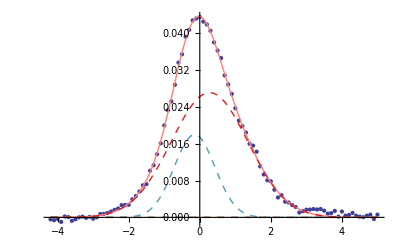

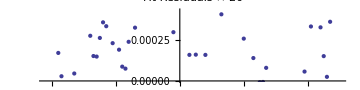

Weights | Means | σs
0.877817 | 11.6026 | 0.414348
0.115623 | -0.151877 | -0.99076
0.006485 | 13.435 | 3.36361
0.0000753876 | -9.50726 | -17.3979

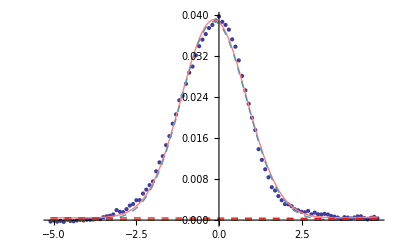

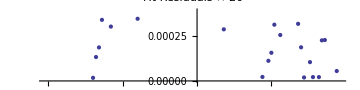

Weights | Means | σs
0.51294 | 0.238279 | 0.51314
0.352976 | -0.130769 | 0.903046
0.0900129 | -0.204124 | -0.175368
0.0440713 | 2.54142 | 0.207285

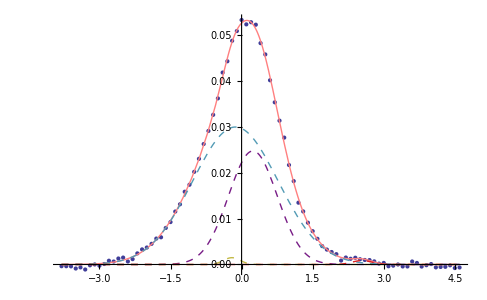

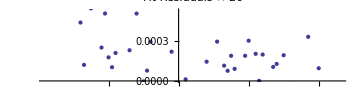

Weights | Means | σs
0.807219 | 10.7525 | -0.756521
0.125975 | 0.12035 | -0.548207
0.00231834 | 2.31598 | 0.609148
0.0644879 | -0.283428 | -0.981845

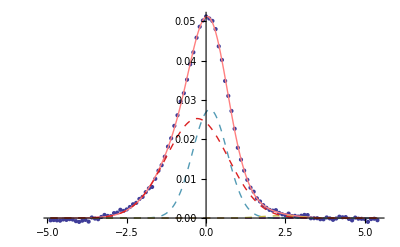

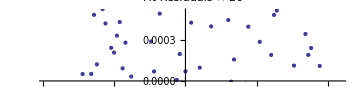

Weights | Means | σs
0.0147522 | 2.78555 | 0.618937
0.34738 | 0.29996 | -0.0583374
0.22703 | -0.318884 | -0.454441
0.410839 | 0.20328 | -0.953926

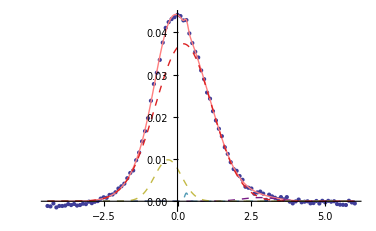

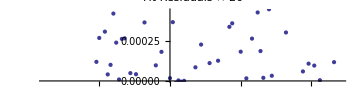

Weights | Means | σs
0.0289677 | 2.25555 | 0.578199
0.125189 | -0.978698 | -0.225096
0.0860259 | -1.83671 | -0.519227
0.759817 | -0.126293 | -0.842279

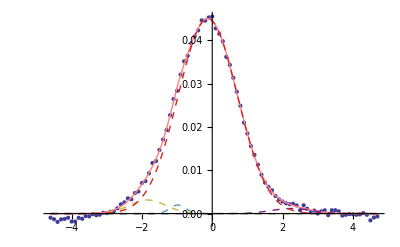

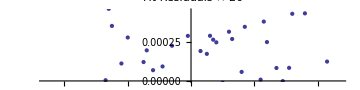

Weights | Means | σs
0.464448 | -0.381064 | -0.920902
0.0280422 | -2.71537 | -0.540104
0.499132 | 0.0693303 | -0.492188
0.00837735 | 1.61538 | 1.55141

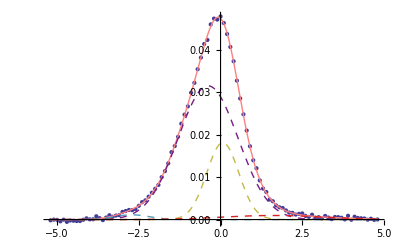

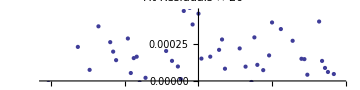

Weights | Means | σs
0.0287496 | 3.01483 | 0.196974
0.53864 | 0.0256113 | -0.594378
0.301555 | -0.384439 | -1.03783
0.131055 | 0.236202 | -0.203541

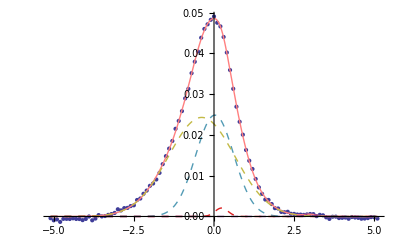

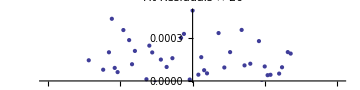

Weights | Means | σs
0.0954932 | -0.315045 | 1.33736
0.315933 | -0.560398 | -0.742172
2.15998×10^-14 | -0.953119 | -1.44442
0.588573 | 0.0996489 | -0.554509

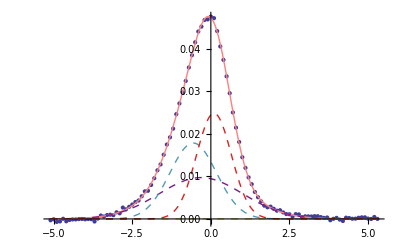

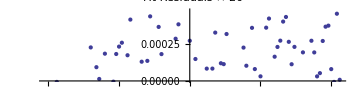

Weights | Means | σs
0.0190485 | 2.86175 | 0.576352
0.416917 | 0.0984633 | -0.461867
0.520846 | -0.232009 | -0.918102
0.0431885 | -2.31937 | -0.650775

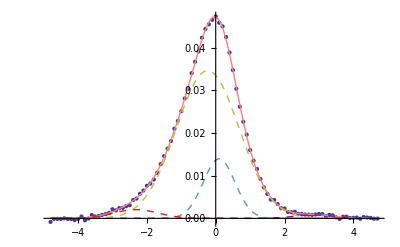

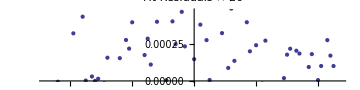

Weights | Means | σs
0.581435 | -11.8226 | -0.906614
0.104051 | 0.278073 | 0.490453
0.141906 | -0.424712 | -1.04415
0.172608 | 23.7779 | 2.54727

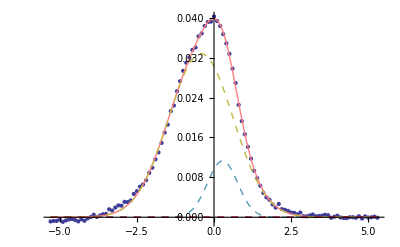

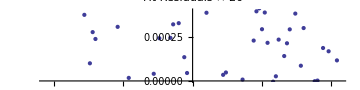

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[FitSummary[CenteredOData[[x]],AllOModels[[x]]],{x,1,Length[CenteredOData],1}]
```

```mathematica
CSummaries=FitSummary/@AllCModels
```

Sum of Squares of Residuals: 9.337931381746313e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.744997
0.219022
0.0230379 | 0.
-0.0640509
1.19796

Sum of Squares of Residuals: 0.000015789585047125255

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0795468
0.023437
0.721449 | -0.44238
1.87065
0.

Sum of Squares of Residuals: 0.000010970222737805098

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0223058
0.135311
0.861331 | 0.971339
-0.187734
0.

Sum of Squares of Residuals: 0.00005383384241342219

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 2.58181×10^-9
0.0635709
0.828646 | -1.58636
0.0750563
0.

Sum of Squares of Residuals: 0.0000920144126208608

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0382415
0.062949
0.724613 | -4.19605
0.175594
0.

Sum of Squares of Residuals: 0.00009023546909026901

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.135727
2.00144×10^-8
0.795269 | -0.18473
1.01665
0.

Sum of Squares of Residuals: 0.00006019181283445589

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.791119
0.0747629
0.0761596 | 0.
129.111
-0.0820984

Sum of Squares of Residuals: 6.510892821174428e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.837577
0.128519
0.0276942 | 0.
-0.19911
0.744366

Sum of Squares of Residuals: 0.000058275679475750086

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 4.95669×10^-9
0.0710014
0.784082 | -3.8044
-0.0425006
0.

Sum of Squares of Residuals: 7.977349352352567e-6

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.836407
0.127068
0.0261622 | 0.
-0.195457
0.811453

Sum of Squares of Residuals: 0.000029385877439711428

| Weights | Centers
Peak 1
Peak 2
Peak 3 | 0.0630375
0.7012
0.0419677 | -0.163819
0.
-4.90177

{{{1.19796,0.0230379},{-0.0640509,0.219022},{0.,0.744997}},{{1.87065,0.023437},{-0.44238,0.0795468},{0.,0.721449}},{{0.971339,0.0223058},{-0.187734,0.135311},{0.,0.861331}},{{-1.58636,2.58181×10^-9},{0.0750563,0.0635709},{0.,0.828646}},{{-4.19605,0.0382415},{0.175594,0.062949},{0.,0.724613}},{{1.01665,2.00144×10^-8},{-0.18473,0.135727},{0.,0.795269}},{{129.111,0.0747629},{-0.0820984,0.0761596},{0.,0.791119}},{{0.744366,0.0276942},{-0.19911,0.128519},{0.,0.837577}},{{-3.8044,4.95669×10^-9},{-0.0425006,0.0710014},{0.,0.784082}},{{0.811453,0.0261622},{-0.195457,0.127068},{0.,0.836407}},{{-4.90177,0.0419677},{-0.163819,0.0630375},{0.,0.7012}}}

Visualize location of peaks and weights:

```mathematica
ListPlot[CSummaries,PlotRange->{{-2.5,2.5},{-0.1,0.5}},PlotMarkers->(StringTake[#,-1]&/@CSheets)]
```

-Graphics-

#### Oxygen Edge

## Multi-peak fitting with generated data

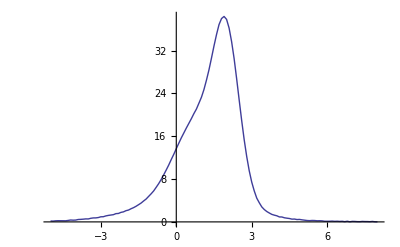

25.1057 ⅇ^(-1.99508 (-1.99902+x)^2)+16.1163 ⅇ^(-0.497021 (-0.990415+x)^2)+3.85703 ⅇ^(-0.116134 (-0.489983+x)^2)

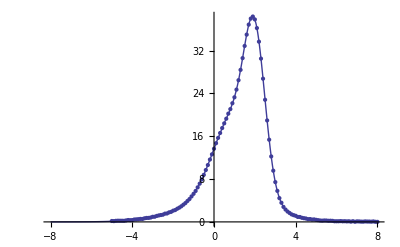

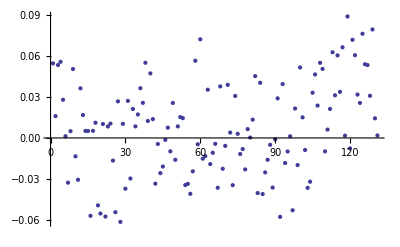

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=Model[data2,3];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

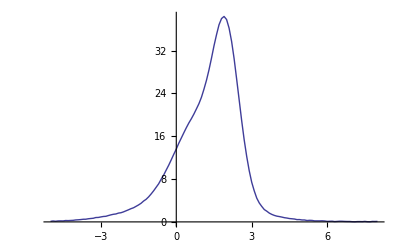

24.9801 ⅇ^(-2.01044 (-1.99924+x)^2)+16.1531 ⅇ^(-0.495882 (-0.99924+x)^2)+3.91041 ⅇ^(-0.118018 (-0.49924+x)^2)

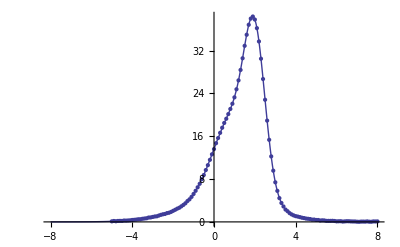

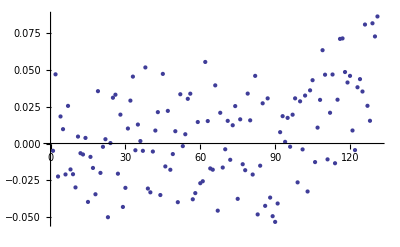

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```

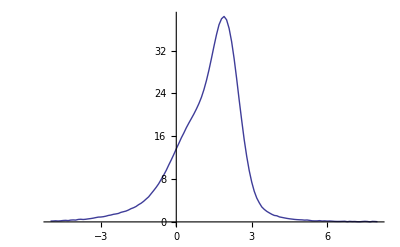

(33.4066 2^(-2.2467 (-1.90903+x)^2))/(1-0.135812 (-1.90903+x)^2)+(1.57346×10^-11 2^(-0.0664325 (-0.909032+x)^2))/(1+0.0354018 (-0.909032+x)^2)+(16.4409 2^(-0.0474042 (-0.409032+x)^2))/(1+1.00537 (-0.409032+x)^2)

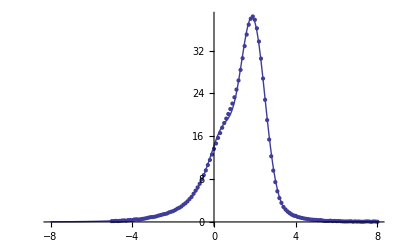

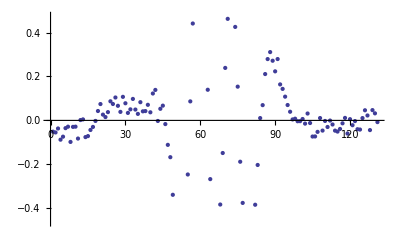

```mathematica
data2=Table[{x,gfn[4,1,1,x]+gfn[5,2,0.5,x]+gfn[2,0.5,2,x]+0.1*RandomReal[]//N},{x,-5,8,0.1}];
ListLinePlot[data2]
nlm2=FixedPeaksVoigtModel[data2,{1,-0.5,0}];
nlm2[x]
Show[Plot[nlm2["Function"][x],{x,-8,8},PlotRange->All],ListPlot[data2,PlotRange->All]]
ListPlot[nlm2["FitResiduals"]]
```